9 Gráficas de funciones
9.1 Gráfica de una o más funciones

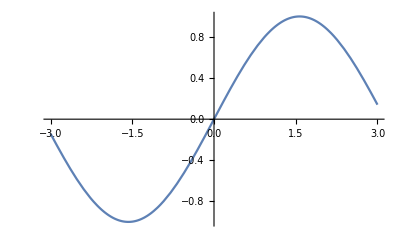

```mathematica
Plot[Sin[x],{x,-3,3}]
```

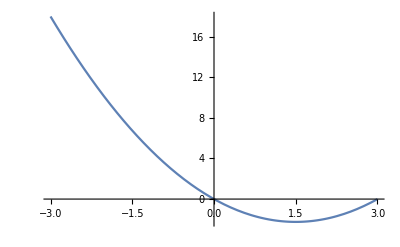

```mathematica
Plot[x^2-3x,{x,-3,3}]
```

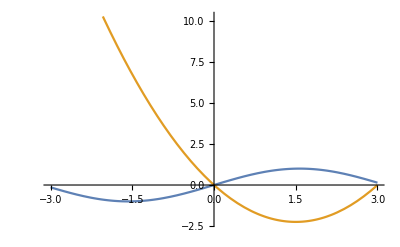

```mathematica
Plot[{Sin[x],x^2-3x},{x,-3,3}]
```

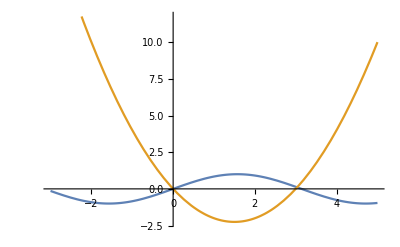

```mathematica
Plot[{Sin[x],x^2-3x},{x,-3,5}]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

9.2 Opciones interesantes

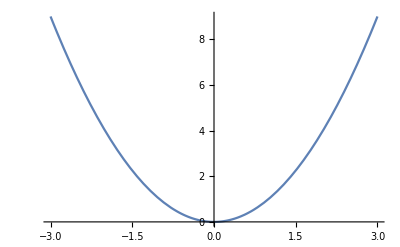

```mathematica
Plot[x^2,{x,-3,3}] (* Proporción aurea *)
```

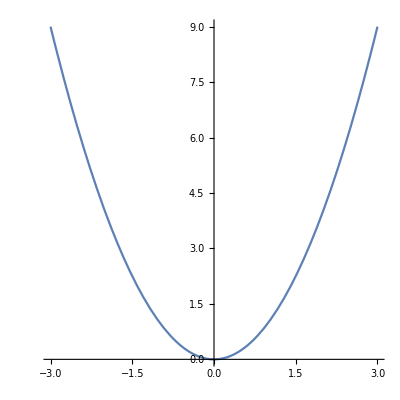

```mathematica
Plot[x^2,{x,-3,3}, AspectRatio->1] (* Proporción uno a uno (Cuadrado) *)
```

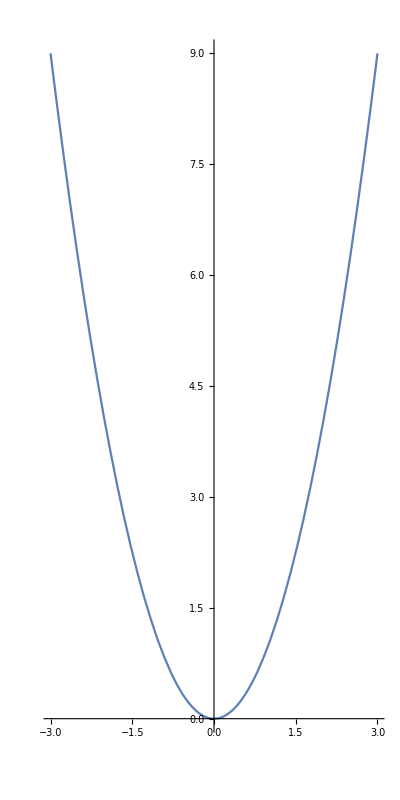

```mathematica
Plot[x^2,{x,-3,3}, AspectRatio->2] (* Proporción dos a uno (Cuadrado) *)
```

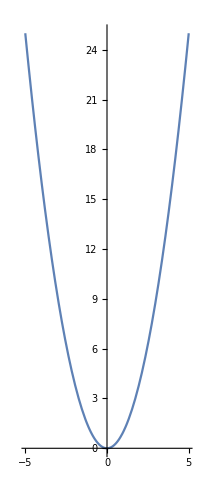

```mathematica
Plot[x^2,{x,-5,5}, AspectRatio->Automatic] (* Ejes del mismo tamaño *)
```

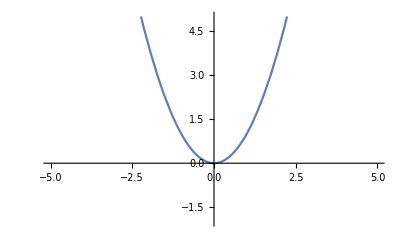

```mathematica
Plot[x^2,{x,-5,5}, PlotRange->{-2,5}]
```

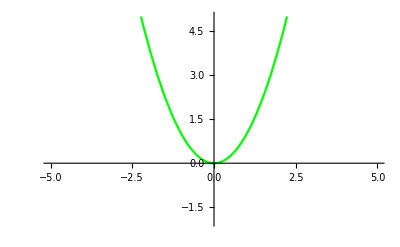

```mathematica
Plot[x^2,{x,-5,5}, PlotRange->{-2,5}, PlotStyle->Green]
```

9.3 Funciones definidas a trozos

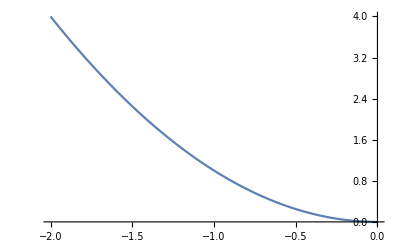

```mathematica
a=Plot[x^2,{x,-2,0}]
```

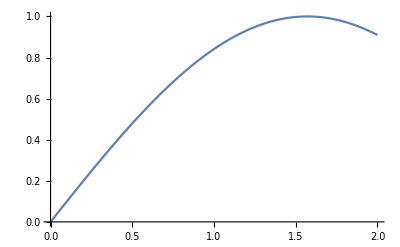

```mathematica
b=Plot[Sin[x],{x,0,2}]
```

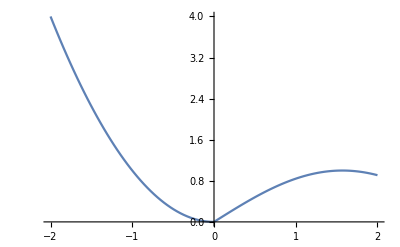

```mathematica
Show[a,b, PlotRange->All] (* Forma no recomendable para funcioens a definidas a trozos *)
```

```mathematica
f[x_]:=Piecewise[{{x^2,-2<x≤0},{Sin[x],0<x≤2}}] (* Forma no recomendable para funcioens a definidas a trozos *)
```

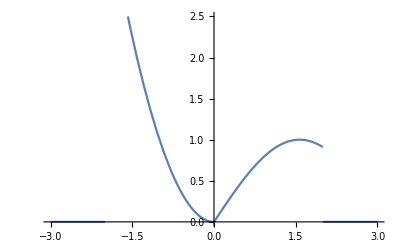

```mathematica
Plot[f[x],{x,-3,3}]
```

9.4 Gráfica de funciones implícitas

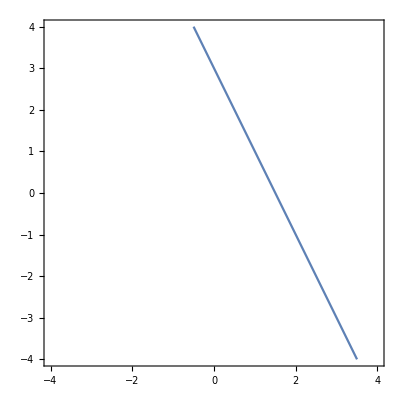

```mathematica
ContourPlot[2x+y==3,{x,-4,4},{y,-4,4}]
```

```mathematica
ContourPlot[2x+y==3,{x,-4,4},{y,-4,4},Axes->True]
```

-Graphics-

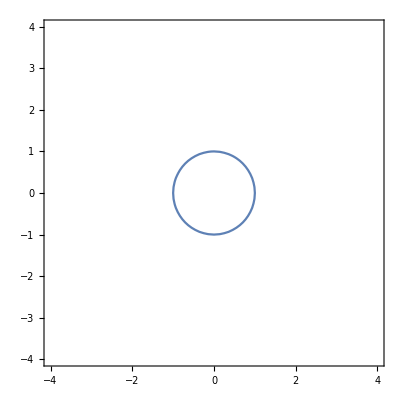

```mathematica
ContourPlot[x^2+y^2==1,{x,-4,4},{y,-4,4},Axes->True]
```

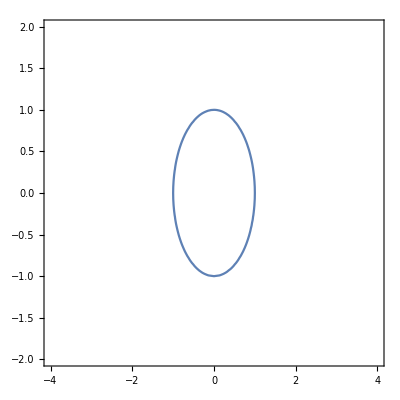

```mathematica
ContourPlot[x^2+y^2==1,{x,-4,4},{y,-2,2},Axes->True] (* Los rangos distorsionan las figura *)
```

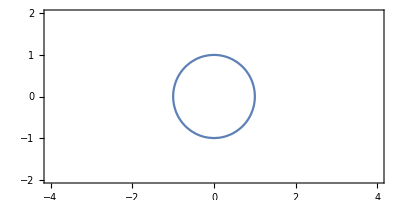

```mathematica
ContourPlot[x^2+y^2==1,{x,-4,4},{y,-2,2},Axes->True, AspectRatio->Automatic]
```

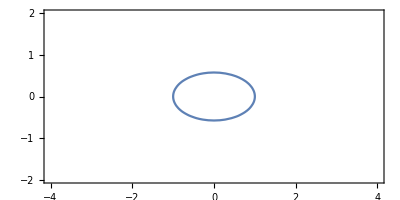

```mathematica
ContourPlot[x^2+3y^2==1,{x,-4,4},{y,-2,2},Axes->True, AspectRatio->Automatic]
```